# Physics through Computational Thinking

## Visual Thinking and Non-dimensionalization

Auditya Sharma and Ambar Jain
Dept. of Physics, IISER Bhopal

Outline

In this lecture you will

1. learn to translate physics problems to represent visually after suitably non-dimensionalizing the equations

2. apply skills of visual thinking to solve a physics problems

3. apply skills of visual thinking to interpret results from graphs

### (non-)Dimensional Analysis and Visualization - The Simple Pendulum

### “The career of a young theoretical physicist consists of treating the harmonic oscillator in ever-increasing levels of abstraction -- Sidney Coleman”

Example 1:  Consider the pendulum of mass m shown in the figure. Find the potential and plot it as a function of θ.

-Graphics-

Solution: [Define] The potential is given by

V(θ)=m g ℓ(1-cos θ)

In order to plot this as a function of θ, we need to convert it into abstract mathematical form by removing physical dimensions from the problem. Its easy! We measure the potential in units of the natural potential scale present in the problem that is m g ℓ. Thus we can re-write the potential as   [Translate]

𝒱(θ)≡(V(θ))/(m g ℓ)=1-cos θ

Now the resulting right hand side is dimensionless and depends only on dimensionless variable θ. Thus we plot our dimensionless potential 𝒱(θ) with respect to θ  [Compute]

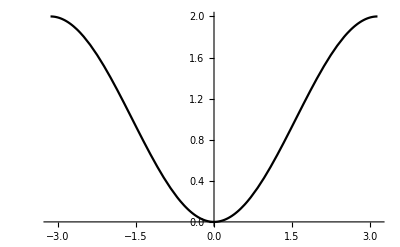

```mathematica
Plot[1-Cos[θ],{θ,-Pi,Pi}]
```

Let me make my plot prettier by labelling the axes and put some styling. I will leave it as an Homework exercise for you to figure out how this is done. Just some tinkering with the code below will help you understand that. [Compute]

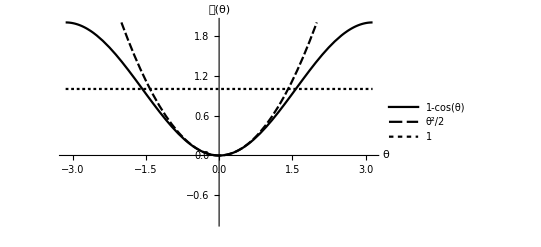

```mathematica
Plot[{1-Cos[θ],θ^2/2,1},{θ,-Pi,Pi},PlotRange->{-1,2},AxesLabel->{Style[θ,16],Style[𝒱[θ],16]},AxesStyle->Thick,TicksStyle->Directive["Label", 14],PlotLegends->"Expressions"]
```

We note that the potential near θ≃0 behaves like a quadratic function with a stable minima, thus we expect the pendulum to behave like Simple Harmonic Oscillator for small oscillations.

Answer the following questions by analyzing the plot [Interpret]

Question: What does 𝒱(θ)=1 represent? What physical value of the potential does it correspond to? What is the angle of maximum deflection θ_max for 𝒱=1.

Question: By eyeballing the picture above estimate the maximum energy of the pendulum for which it may still qualify for a simple harmonic oscillator.

Question: By eyeballing the picture above estimate the maximum deflection angle θ_max for which the pendulum may still qualify for a simple harmonic oscillator.

### (non-)Dimensional Analysis and Visualization - 2

Example 2: Consider the following problem from your course on Mechanics. A man throws a ball from the top of the hill of height h and angle of inclination ϕ, as shown in the figure below. Lets assume that the ball is thrown at an angle θ with speed v. Ignore the height of the man compared to the hill. Find the distance x_0 where the ball hits the hill slope for the first time. For what values of θ, ϕ, v and h there is a solution? Under what condition there is no solution? Explore the problem visually using graphics.

-Graphics-

Define: First we need to lay out a coordinate system.

-Graphics-

1. We identify the trajectory of the ball as a quadratic function from the information that projectiles follow parabolic trajectories or more appropriately that most general trajectory of a particle under constant acceleration is parabolic. Thus, we can write:

y_ball(x)=a x^2+b x +c

2. Equation of the hill is represented by a straight line

y_hill(x)=α x+β

3. We need to determine coefficients, a, b, c, α and β by using some known data points. After that intersection of these two lines give me a solution.

Translate: Now we will extract appropriate information out of the problem and so that we can compute these coefficients and find second point of intersection. We will express this information in mathematical form:

(i) Position:         y_ball(0)=h

(ii) Velocity:       ((ⅆ y_ball)/(ⅆ t)|)_(x=0)=v sin θ

(iii) Acceleration:   ((ⅆ^2 y_ball)/(ⅆ t^2)|)_(x=0)=-g

(iv) Hill Top:   y_hill(0)=h

(v)  Hill Angle:   (ⅆy_hill(0))/ⅆx=-tan ϕ

Compute: Using the five pieces of information we can determine the coefficients a,b, c, α and β.

(i) |    ⇒    | c=h
(ii) |    ⇒    | b= tan θ
(iii) |   ⇒   | a=-g/(2 v^2 cos^2 θ)
(iv) |   ⇒   | β=h
(v) | ⇒ | α=-tan ϕ

The equations now become

y_ball(x)=-g/(2 v^2 cos^2 θ) x^2+tan θ x +h

y_hill(x)=-tan ϕ x+h

At this point you can solve for intersection of two curves and find where they intersect next. We will explore this problem by visualization and and cross-check with analytical result.

h is the only length scale in the problem, so we will non-dimensionalize y and x in units of h so that we can make a plot. This gives

(y_ball(x))/h=(-g h)/(2 v^2 cos^2 θ) (x/h)^2+tan θ x/h +1
⇒  Y_ball(X)=-γ/(cos^2 θ)X^2+tan θ  X+1

where Y and X are dimensionless coordinates measured in units of h, and γ= (g h)/(2 v^2). For the hill, we get

(y_hill(x))/h=-tan ϕ x/h+1
⇒  Y_hill(X)=-tan ϕ X+1

To summarize, the two abstract equations that we are dealing with now are

Y_ball(X)=-γ/(cos^2 θ)X^2+tan θ  X+1
Y_hill(X)=-tan ϕ X+1

which have got three independent dimensionless parameters: γ, θ and ϕ.  Few things to note here:

γ is a measure of inverse of speed in units of √(g h).

All the dimensionless parameters that define the problem for physically relevant values are typically order 1 numbers. Its always easy to analyze a problem in terms of order 1 numbers.

The effects created by changing v and h are not independent. γ can be changed either by changing v or h.

Interpret: We will now plot and interpret our results:

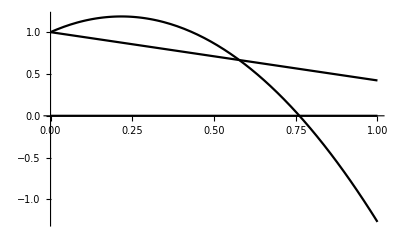

```mathematica
Plot[{-γ/Cos[θ]^2 x^2+Tan[θ]x +1,-Tan[ϕ]x+1,0}/.{ϕ->Pi/6,θ->Pi/3,γ->1},{x,0,1}]
```

```mathematica
Manipulate[Plot[{-γ/Cos[θ]^2 x^2+Tan[θ]x +1,-Tan[ϕ]x+1,0},{x,0,2},PlotRange->{0,2}],{{ϕ,Pi/6},0,Pi/2},{{θ,Pi/3},0,Pi/2},{{γ,1},1/2,2}]
```

Homework:

(a) Find X_0 and x_0 for a given θ,, ϕ and γ.

(b) For a fixed θ and ϕ, Find the critical value of γ below which there is no solution. Verify that the plot above agrees with your result.

### Parametric plot for trajectory

Example (Problem adapted from Kleppner & Kolenkow): A bead moves outward with constant speed u along the spoke of a wheel. It starts from the center at t=0. The angular position of the spoke is given by θ=ω t, where ω is constant. Find the trajectory of the particle and plot it.

Solution: Velocity and Acceleration in the polar coordinates is given by

v⃗=ṙ r̂+r θ̇ θ̂
a⃗=(r^(..) -r (θ̇)^2)r̂+(r θ^(..)+2 ṙ θ̇)θ̂

From the problem we identify

ṙ=u
θ̇=ω
r=u t
θ = ω t

For trajectory, we have

x=r cos(θ) = u t cos(ω t)
y=r sin(θ)=u t sin(ω t)

We non-dimensionalize time and distance by noting that 1/ω is constant with dimensions of time while u/ω is a constant with dimensions of distance. Thus we can define,

X= ω/u x
Y=ω/u y
T=ω t

Therefore, in terms of dimensionless variables

X= T cos(T)
Y=T sin(T)

We plot the trajectory using ParametricPlot function:

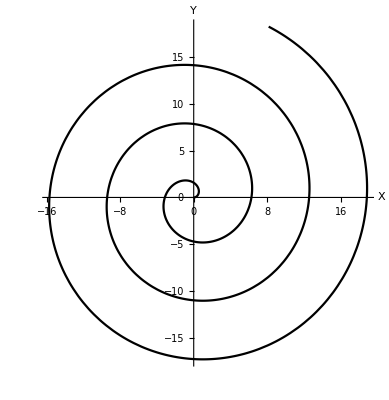

```mathematica
ParametricPlot[{T Cos[T],T Sin[T]},{T,0,20},AxesLabel->{"X","Y"}]
```

After non-dimensionalization, the equation for trajectory became scaleless and we got a unique solution.

Question: Interpret what is the effect of changing ω and u on this trajectory?  This one solution in the plot contains all the solutions corresponding to various values of u and ω. Can you explain how?

### Zeros, divergences, extrema and asymptotes

Zero: A function f(x) has zeros at points x^* where f(x^*)=0. Identifying these points should be the first step in sketching a function.

f(x)=x^2-3x+2
= (x-2)(x-1).

Factorization (when possible) helps immediately identify the zeros.

```mathematica
Plot[x^2-3x+2,{x,0,3}];
```

Divergence: A function f(x) has divergences (or singularities) at points x^* where 1/(f(x^*))has a zero. Identifying these points (and sometimes the form of the divergence nearby) helps us figure out where and how the function blows up.

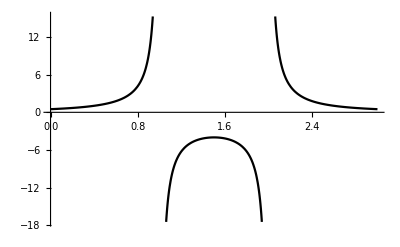

```mathematica
Plot[1/((x-1)(x-2)),{x,0,3}]
```

Extrema: A function f(x) has extrema at points x^* where f'(x^*)=0. Further work would be essential to clarify if the point is a minimum or a maximum or an inflection point. Identifying these points help in getting the broad shape of the function. Let us take the example of the same function f(x)=x^2-3x+2. Here it turns out that rather than factorization, it is more useful to `complete the squares’.

f(x)=x^2-3x+2
= (x-3/2)^2-1/4.

```mathematica
Plot[x^2-3x+2,{x,0.5,2.5},PlotRange->{-0.3,0.3}];
```

Asymptote: An asymptote is a curve that a function f(x) approaches arbitrarily closely in some limit. A familiar example is the curve f(x)= 1/x, which asymptotically approaches the X-axis as x→∞, and asymptotically approaches the Y-axis as x→0.

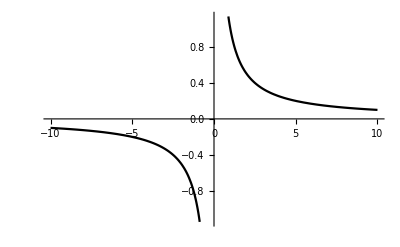

```mathematica
Plot[1/x,{x,-10,10}]
```

Let’s increase the y-range of the plot and examine it whether the curve 1/x approaches y-axis. We will do this by invoking an option for the Plot function called PlotRange

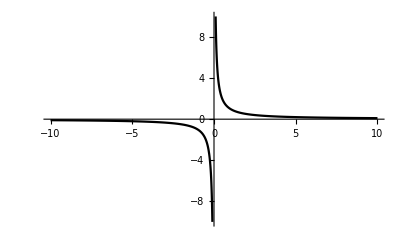

```mathematica
Plot[1/x,{x,-10,10},PlotRange->{-10,10}]
```

### Homework

1.  Consider an infinite inclined plane that makes an angle α with the horizontal as shown in the figure below. A ball is dropped vertically from above this inclined plane. It travels a height h before it strikes the inclined plane for the first time. Find the length l_1 along the inclined plane between the points where the ball strikes for the first time and second time.  You need to first non-dimensionalize the equations and plot the graphs involved. Can you generalize to find the distance l_n between the points where the ball strikes for the n^thand the n+1^th times?. Consider all collisions to be elastic.

-Graphics-

Hints: The first part of the problem actually works out to a special case of the hill problem worked out in class. The first step is to figure out with some geometry tricks, what is the angle corresponding to what was called θ in the hill problem. The non-dimensionalization works even more cleanly than in the hill problem, because you will eventually end up with just one parameter α.

The second part of the problem is more tricky, since you would have to find the angle at which the quadratic trajectory intersects the linear curve at various intersections. Is there a pattern you can see? After you have struggled a bit with a direct approach (potentially successfully!), think of what other coordinate system this problem might be better handled in!